```mathematica
<<NDSolve`FEM`
```

```mathematica
(*Function to generate a sphere at radius r*)
generateSphereElementMesh[r_]:=Module[{},
(*Create a discretized sphere*)
ToElementMesh[Sphere[{0,0,0},r]]
];
```

```mathematica
(*Define the number of keyframes*)
numKeyframes=10;

(*Generate keyframes for spheres with radii interpolating from 1 to 10*)
radii=Table[1+(10-1)*t,{t,0,1,1/(numKeyframes-1)}];
sphereEMs=generateSphereElementMesh[#]&/@radii;
```

```mathematica
Table[sphereEMs[[i]]["Wireframe"],{i,1,Length[sphereEMs]}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
SetDirectory@NotebookDirectory[]

Export["mesh.csv",sphereEMs[[1]]["Coordinates"]]
```

/home/graveltr/github/kerr-ray-tracing

mesh.csv

```mathematica
innerRadius=6;
outerRadius=7;

SetDirectory@NotebookDirectory[]
concentricRegionOne=RegionPlot3D[innerRadius^2<x^2+y^2+z^2<outerRadius^2&&y==0,{x,-outerRadius,outerRadius},{y,-outerRadius,outerRadius},{z,-outerRadius,outerRadius}]
Export["./models/concentricSphereAnimation/concentricRegionOne.obj",concentricRegionOne];
```

/home/graveltr/github/kerr-ray-tracing

-Graphics3D-

```mathematica
ParametricPlot3D[{u Cos[v],u Sin[v],0 },{u,0.5,1},{v,0,2π}]
```

-Graphics3D-

```mathematica
outerRadius=3;
innerRadius=1;
uRange={0,2 Pi};
uSteps=50; (*number of steps in u direction*)

Graphics3D[Table[With[{vmax=Min[2 Pi,u+Pi/2]},(*Compute the maximum range for v based on u*)ParametricPlot3D[{(innerRadius+(outerRadius-innerRadius) u/localU) Cos[v],(innerRadius+(outerRadius-innerRadius) u/localU) Sin[v],0},{u,localU,localU+0.001},{v,0,vmax},Mesh->None,PlotStyle->Directive[Blue,Opacity[0.7]]]],{localU,First[uRange],Last[uRange],(Last[uRange]-First[uRange])/uSteps}]]
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

-Graphics3D-

```mathematica
Graphics3D[
Table[
ParametricPlot3D[{r Cos[v],r Sin[v],0},
{r,rLocal,rLocal+0.001},
{v,-((π/2)Sin[π (rLocal-1)]+(π/2))+π,(π/2)Sin[π (rLocal-1)]+(π/2)},Mesh->None,PlotStyle->Directive[Blue,Opacity[0.7]]
],
{rLocal,1.1,2,0.1}
]
]
```

-Graphics3D-

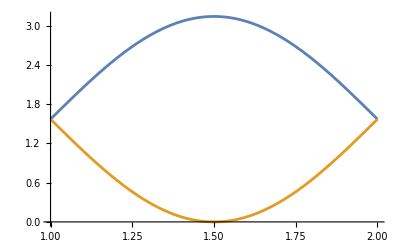

```mathematica
Plot[{(π/2)Sin[π (x-1)]+(π/2),-((π/2)Sin[π (x-1)]+(π/2))+π},{x,1,2}]
```

```mathematica
Clear[r]
plots=Table[
ParametricPlot3D[{r Cos[v],r Sin[v],0},
{r,rLocal,rLocal+0.001},
{v,-((π/2)Sin[π (rLocal-1)]+(π/2))+π,(π/2)Sin[π (rLocal-1)]+(π/2)},Mesh->None]
,
{rLocal,5,10,0.01}
];

(*Convert ParametricPlot3D objects to Graphics3D objects and combine them*)
```

```mathematica
Clear[r]
plot1=ParametricPlot3D[{u Cos[v],u Sin[v],0},{u,1,2},{v,0,2π}]
plot2=ParametricPlot3D[{u Cos[v],u Sin[v],0},{u,3,4},{v,0,2π}]
combinedPlot=Show[plot1,plot2,PlotRange->{{-5,5},{-5,5},{-5,5}}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
combinedPlot=Show[plot1,plot2]
```

-Graphics3D-

```mathematica
SetDirectory@NotebookDirectory[]
Export["./models/concentricSphereAnimation/concentricRegionOne.obj",combinedPlot];
```

/home/graveltr/github/kerr-ray-tracing

```mathematica
combinedPlot=Show[plots,PlotRange->{{-10,10},{-10,10},{-10,10}}]
```

-Graphics3D-

```mathematica
RegionPlot3D[0<=y<=1&&5<=x^2+z^2<=10,{x,-4,4},{y,-4,4},{z,-4,4}]
Export["./models/concentricSphereAnimation/concentricRegionOne.obj",%];
```

-Graphics3D-

```mathematica
Clear[radialBounds,uplus,getληCritical,θplus,θminus]
Δ[M_,a_][r_]:=r^2-2 M r +a^2
(* The photon sphere radial bounds *)
radialBounds[M_,a_]:=Module[{},
{2 M (1+Cos[2/3 ArcCos[-a/M]]),2 M (1+Cos[2/3 ArcCos[a/M]])}
]
uplus[M_,a_][η_,λ_]:=Module[{Δθ},
Δθ=(1/2)(1-(η+λ^2)/a^2);
Δθ+√(Δθ^2+η/a^2)
]
(* Obtain the critical values of conserved quantities at a given radius in the photon sphere *)
(* Returns λ, η in that order. *)
getληCritical[M_,a_][rc_]:=Module[{},
{a+rc/a(rc-(2Δ[M,a][rc])/(rc-M)),rc^3/a^2((4M Δ[M,a][rc])/(rc-M)^2-rc)}
]
θplus[M_,a_][η_,λ_]:=Module[{},
ArcCos[-√(uplus[M,a][η,λ])]
]
θminus[M_,a_][η_,λ_]:=Module[{},
ArcCos[√(uplus[M,a][η,λ])]
]
```

```mathematica
Clear[M,a]
M=1;
a=0.9;
radialBounds[M,a]
{λc,ηc}=getληCritical[M,a][2.0]
θminus[M,a][ηc,λc]
θplus[M,a][ηc,λc]
```

{1.55785,3.91027}

{1.74444,12.2469}

0.452102

2.68949

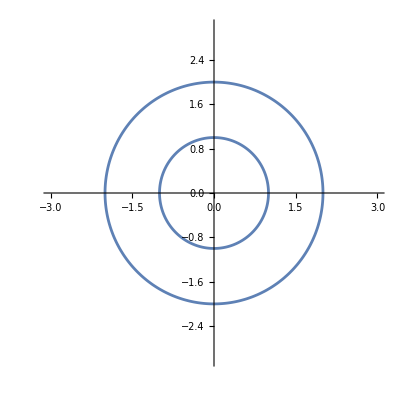

```mathematica
plot1=ParametricPlot[{Cos[u],Sin[u]},{u,0,2π}];
plot2=ParametricPlot[2{Cos[u],Sin[u]},{u,0,2π}];
Show[plot1,plot2,PlotRange->{{-3,3},{-3,3}}]
```

```mathematica
Clear[M,a]
M=1;

photonShellKeyframes=Module[{λc,ηc,rminus,rplus},
Table[
{rminus,rplus}=radialBounds[M,a];
Table[
{λc,ηc}=getληCritical[M,a][rc];
ParametricPlot3D[{rc Sin[θ],0,rc Cos[θ]},{θ,θminus[M,a][ηc,λc],θplus[M,a][ηc,λc]}]
,{rc,rminus+0.1,rplus-0.1,0.05}
]
,{a,0.5,0.9,0.005}]
];
```

```mathematica
Manipulate[Show[photonShellKeyframes[[f]],PlotRange->{{-4,4},{-4,4},{-4,4}}],{f,1,Length[photonShellKeyframes],1}]
```

Part::partd: Part specification photonShellKeyframes[[81]]
     is longer than depth of object.

Show::gtype: Part is not a type of graphics.

```mathematica
SetDirectory@NotebookDirectory[]

basePath="./models/photonShellAnimation/";
For[i=1,i<=Length[photonShellKeyframes],i++,
Export[basePath<>"photon-shell-keyframe-"<>ToString[i]<>".obj",Show[photonShellKeyframes[[i]]]];
]
```

/home/graveltr/github/kerr-ray-tracing

-Graphics3D-